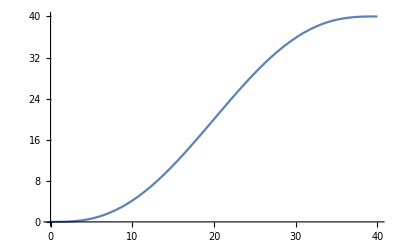

```mathematica
tf=40;(*the total shuttling time*)
Plot[(10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5)*40,{t,0,40}]
```

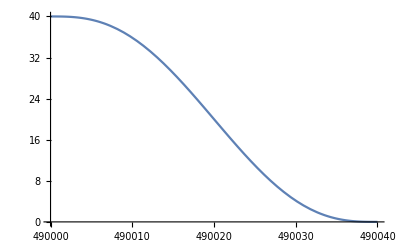

```mathematica
tf=40;(*the total shuttling time*)
Plot[(10*((490040-t)/tf)^3-15*((490040-t)/tf)^4+6*((490040-t)/tf)^5)*40,{t,490000,490040}]
```

```mathematica
Plot[(10*(t/40)^3-15*(t/40)^4+6*(t/40)^5)*40,{t,0,40}]
```

-Graphics-

```mathematica
10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5
```

t^3/6400-(3 t^4)/512000+(3 t^5)/51200000

```mathematica
Simplify[t^3/6400-(3 t^4)/512000+(3 t^5)/51200000]
```

(t^3 (8000-300 t+3 t^2))/51200000

```mathematica
8000-300 t+3 t^2
```

8000-300 t+3 t^2

```mathematica
FullSimplify[8000-300 t+3 t^2]
```

8000+3 (-100+t) t

```mathematica
FourierSeries[10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5,t,5]
```

-(3 π^4)/2560000+(ⅈ ⅇ^(-ⅈ t) ((-47640+7200 ⅈ)+(7940-1200 ⅈ) π^2+3 π^4))/51200000-(ⅈ ⅇ^(ⅈ t) ((-47640-7200 ⅈ)+(7940+1200 ⅈ) π^2+3 π^4))/51200000-(ⅈ ⅇ^(-2 ⅈ t) ((-23955+1800 ⅈ)+(15970-1200 ⅈ) π^2+6 π^4))/204800000+(ⅈ ⅇ^(2 ⅈ t) ((-23955-1800 ⅈ)+(15970+1200 ⅈ) π^2+6 π^4))/204800000+(ⅈ ⅇ^(-3 ⅈ t) ((-47960+2400 ⅈ)+(71940-3600 ⅈ) π^2+27 π^4))/1382400000-(ⅈ ⅇ^(3 ⅈ t) ((-47960-2400 ⅈ)+(71940+3600 ⅈ) π^2+27 π^4))/1382400000-(ⅈ ⅇ^(-4 ⅈ t) ((-95955+3600 ⅈ)+(255880-9600 ⅈ) π^2+96 π^4))/6553600000+(ⅈ ⅇ^(4 ⅈ t) ((-95955-3600 ⅈ)+(255880+9600 ⅈ) π^2+96 π^4))/6553600000+(ⅈ ⅇ^(-5 ⅈ t) ((-239928+7200 ⅈ)+(999700-30000 ⅈ) π^2+375 π^4))/32000000000-(ⅈ ⅇ^(5 ⅈ t) ((-239928-7200 ⅈ)+(999700+30000 ⅈ) π^2+375 π^4))/32000000000

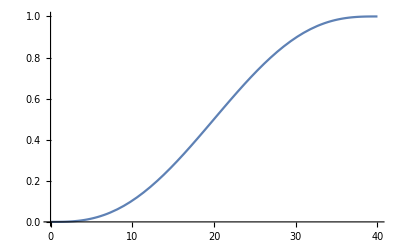

```mathematica
Plot[10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5,{t,0,40}]
```

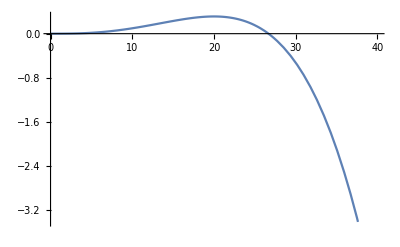

```mathematica
Plot[10*(t/tf)^3,{t,0,40}]
```

```mathematica
10/0.00004^3
```

```mathematica
tf
```

40

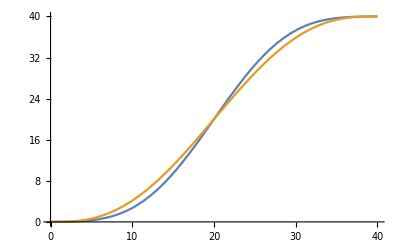

```mathematica
L=40;T=40;Plot[{L/2(1-10/9(cos(πt/T)-0.1cos((3πt)/T))),(10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5)*40},{t,0,40}]
```

```mathematica
L/2(1-10/9(cos(πt/T)-0.1cos((3πt)/T)))
```

20 (1-10/9 (Cos[(π t)/40]-0.1 Cos[(3 π t)/40]))

```mathematica
Plot[{20*(1-(10/9)*(Cos[(Pi*t)/40]-0.1*Cos[(3*Pi*t)/40])),(10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5)*40},{t,0,40}]
```

-Graphics-

```mathematica
k1=10
k2=0.375
k3=0.00375
```

10

0.375

0.00375

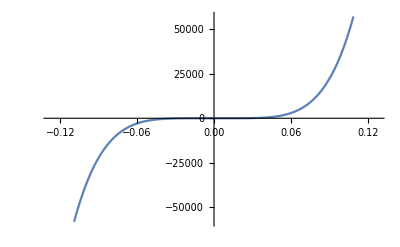

```mathematica
Plot[10 t^3+375000. t^4+3.75*^9 t^5,{t,-0.127622,0.127582}]
```

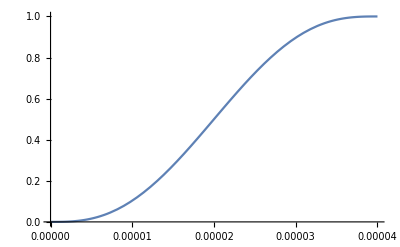

```mathematica
tf=40*10^-6;Plot[{(10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5)},{t,0,tf}]
```

```mathematica
(10*(t/tf)^3-15*(t/tf)^4+6*(t/tf)^5)
```

156250000000000 t^3-5859375000000000000 t^4+58593750000000000000000 t^5

```mathematica
CoefficientList[156250000000000 t^3-5859375000000000000 t^4+58593750000000000000000 t^5,{t}]
```

{0,0,0,156250000000000,-5859375000000000000,58593750000000000000000}

```mathematica
156250000000000
```

156250000000000

```mathematica
ScientificForm[N[156250000000000,15]]
```

1.56250000000000×10^14

```mathematica
-5859375000000000000
```

-5859375000000000000

```mathematica
ScientificForm[N[-5859375000000000000,19]]
```

-5.859375000000000000×10^18

```mathematica
58593750000000000000000
```

58593750000000000000000

```mathematica
ScientificForm[N[58593750000000000000000,23]]
```

5.8593750000000000000000×10^22

```mathematica
k1=1.562*10^14
k2=-5.86*10^18
k3=5.86*10^22
k1*(t^3)+k2*(t^4)+k3*(t^5)
```

1.562×10^14

-5.86×10^18

5.86×10^22

1.562×10^14 t^3-5.86×10^18 t^4+5.86×10^22 t^5

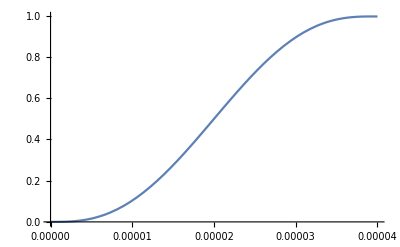

```mathematica
Plot[1.562*^14 t^3-5.86*^18 t^4+5.860000000000001*^22 t^5,{t,0,0.00004}]
```

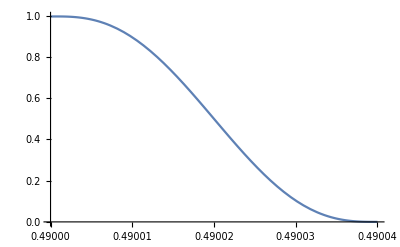

```mathematica
Plot[1.562*^14 *(0.49004-t)^3-5.86*^18 *(0.49004-t)^4+5.860000000000001*^22 *(0.49004-t)^5,{t,0.49,0.49004}]
```